```mathematica
SetDirectory[NotebookDirectory[]];
```

## Import Neural Data and Normalize

```mathematica
cp1=Transpose[Import["nn_state_74.csv"]];
```

```mathematica
Dimensions[cp1]
```

{25,620}

```mathematica
ma=Table[Max[cp1[[x]]],{x,1,25}];
mi=Table[Min[cp1[[x]]],{x,1,25}];
ma-mi
```

{1.99981147645890334,1.97432548965505816,10.7974903697326177,0.20818,0.978788582458009926,0.120333747316905645,1.53612764080853481,1.54569941164623115,1.52026545461056217,1.,38.3829,17.7256,0.,84.5678,12.5365,137.45,4.4087,0.849003,363.807,227.033,0.99999999905265113,1.,1.,1.,0.998459}

```mathematica
x=1;s1= (cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]]);
x=2;s2=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=3;s3=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]]);
x=4;s4= (cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]]);
x=5;s5=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=6;s6=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]]);
x=7;s7= (cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]]);
x=8;s8=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=9;s9=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]]);
x=10;s10=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]]);
x=11;h1= (cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=12;h2=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=13;h3=cp1[[x]];
x=14;h4= (cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=15;h5=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=16;h6=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]]);
x=17;h7= (cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=18;h8=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=19;h9=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]]);
x=20;h10=(cp1[[x]] - Min[cp1[[x]]])/(Max[cp1[[x]]] -Min[cp1[[x]]] );
x=21; o1= cp1[[x]];
x=22; o2= cp1[[x]];
x=23; o3= cp1[[x]];
x=24; o4= cp1[[x]];
x=25; o5= cp1[[x]];
```

```mathematica
activationI=1-{s1,s2,s3,s4,s5,s6,s7,s8,s9,s10};
activationH1=1-{h1,h2,h3,h4,h5};
activationH2=1-{h6,h7,h8,h9,h10};
activationO=1-{o1,o2,o3,o4,o5};
```

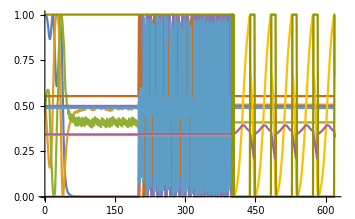

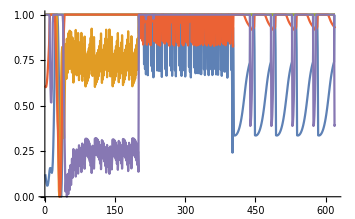

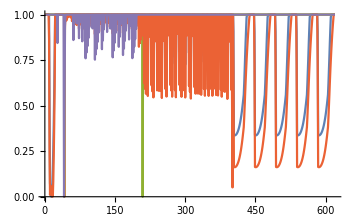

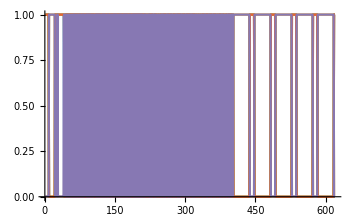

```mathematica
ListLinePlot[activationI,PlotRange->All]
ListLinePlot[activationH1,PlotRange->All]
ListLinePlot[activationH2,PlotRange->All]
ListLinePlot[activationO,PlotRange->All]
```

## Neural activations

#### Parameters (duration, number of neurons, size of disks, distance between disks)

```mathematica
duration=Dimensions[cp1][[2]];
numI=10;
numO=5;
radIO=0.5;
distIO =2.5  radIO;
numH=5;
radH = 0.7;
distH = 2.5 radH;
```

#### Neuron (x,y) positions

```mathematica
posI = Table[{-3,y},{y,distIO ((numI-1)/2),-distIO  ((numI-1)/2),-distIO}];
posH1 = Table[{-1,y},{y,distH ((numH-1)/2),-distH  ((numH-1)/2),-distH}];
posH2 = Table[{1,y},{y,distH ((numH-1)/2),-distH  ((numH-1)/2),-distH}];
posO = Table[{3,y},{y,distIO ((numO-1)/2),-distIO  ((numO-1)/2),-distIO}];
```

#### Generate figures

```mathematica
plots=Table[
Show[
{
Graphics[Table[{EdgeForm[Thick],GrayLevel[activationI[[x]][[t]]],Disk[posI[[x]],radIO]},{x,1,10}]],
Graphics[Table[{EdgeForm[Thick],GrayLevel[activationH1[[x]][[t]]],Disk[posH1[[x]],radH]},{x,1,5}]],
Graphics[Table[{EdgeForm[Thick],GrayLevel[activationH2[[x]][[t]]],Disk[posH2[[x]],radH]},{x,1,5}]],
Graphics[Table[{EdgeForm[Thick],GrayLevel[activationO[[x]][[t]]],Disk[posO[[x]],radIO]},{x,1,5}]]
}
]
,{t,1,duration,1}
];
```

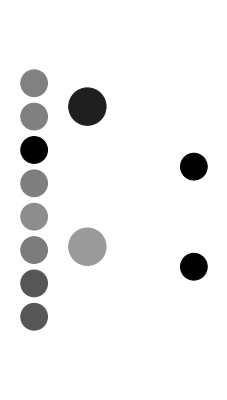

```mathematica
plots[[1]]
```

#### Compile figures into animation and export

```mathematica
Export["animate.mp4",plots,FrameRate->15]
```

animate.mp4

## Import Body Data

```mathematica
b=Transpose[Import["body_state_74.csv"]];
```

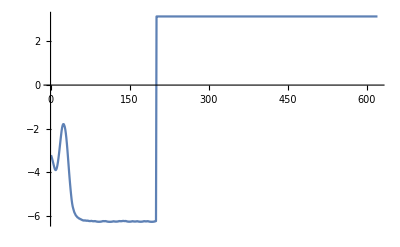

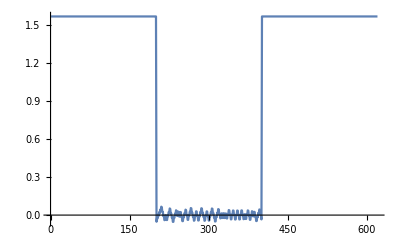

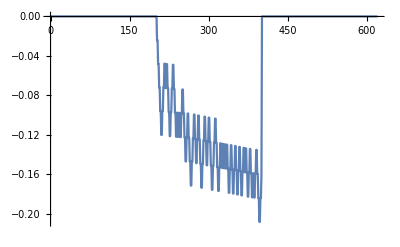

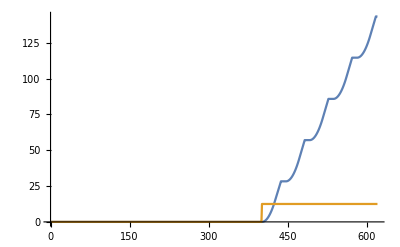

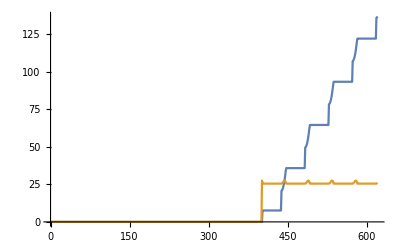

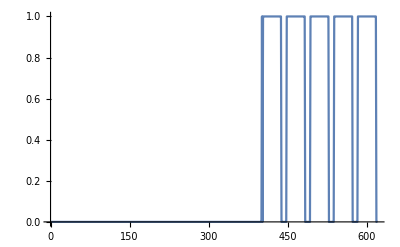

```mathematica
ListLinePlot[b[[1]],PlotRange->All]
ListLinePlot[b[[2]],PlotRange->All]
ListLinePlot[b[[3]],PlotRange->All]
ListLinePlot[{b[[4]],b[[5]]},PlotRange->All]
ListLinePlot[{b[[6]],b[[7]]},PlotRange->All]
ListLinePlot[b[[8]],PlotRange->All]
```

## Inverted Pendulum

#### Plot the pendulum over time

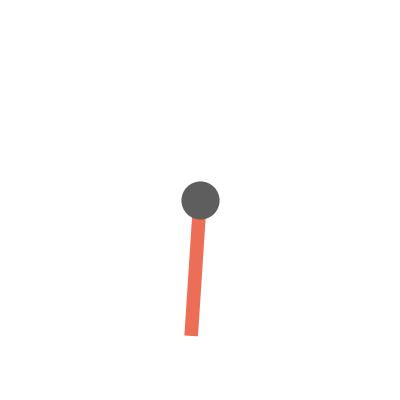

```mathematica
plots=Table[
Show[
{
Graphics[{RGBColor["#ED6E57"],Rotate[Rectangle[{-0.25,0},{0.25,5},RoundingRadius->0.3],b[[1]][[t]] ,{0,0}]}],
Graphics[{RGBColor["#5E5E5E"],Disk[{0,0},0.7]}]
},PlotRange->{{-6,6},{-6,6}}
],{t,1,duration,1}
];
plots[[1]]
```

#### Compile figures into animation and export

```mathematica
Export["animateIP.mp4",plots,FrameRate->15]
```

animateIP.mp4

## Cartpole

#### Plot the pendulum over time

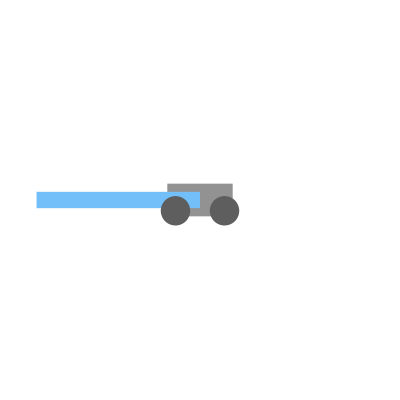

```mathematica
plots=Table[
Show[
{
Graphics[{RGBColor["#929292"],Rectangle[{-1+b[[3]][[t]],-0.5},{1+b[[3]][[t]],.5},RoundingRadius->0.3]}],
Graphics[{RGBColor["#73BFF9"],Rotate[Rectangle[{-0.25+b[[3]][[t]],0},{0.25+b[[3]][[t]],5},RoundingRadius->0.3],b[[2]][[t]] ,{0,0}]}],
Graphics[{RGBColor["#5E5E5E"],Disk[{-0.75+b[[3]][[t]],-0.33},0.45]}],
Graphics[{RGBColor["#5E5E5E"],Disk[{0.75+b[[3]][[t]],-0.33},0.45]}]
},PlotRange->{{-5,5},{-5,5}}
],{t,1,duration,1}
];
plots[[1]]
```

#### Compile figures into animation and export

```mathematica
Export["animateCP.mp4",plots,FrameRate->15]
```

animateCP.mp4

## Legged walker

### Initialization

```mathematica
$Head={{29.4,0},{21.9,11.25},{14.4,0},{21.9,-11.25},{29.4,0}};$Torso={{18,6},{0,12},{-30,5},{-30,-5},{0,-12},{18,-6}};$LeftAnt={{25.65,-5.6},{65,-30}};$RightAnt={{25.65,5.6},{65,30}};$LeftCercus={{-30,-2},{-34,-8}};$RightCercus={{-30,2},{-34,8}};
```

```mathematica
DisplayBody[{JointX_,JointY_,FootX_,FootY_,FootState_}]:=
Module[{Head,Torso,LeftAnt,RightAnt,LeftCercus,RightCercus,Leg,Foot},
Head=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$Head];
Torso=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$Torso];
LeftAnt=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$LeftAnt];
RightAnt=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$RightAnt];
LeftCercus=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$LeftCercus];
RightCercus=Map[{#⟦1⟧+JointX,#⟦2⟧}&,$RightCercus];
Leg={{JointX,JointY},{FootX,FootY}}; 
Foot={FootX,FootY};
Show[
Graphics[
{{RGBColor["#81D653"],Polygon[Head],Polygon[Torso]},{RGBColor["#5D963C"],Line[LeftAnt],Line[RightAnt],Line[LeftCercus],Line[RightCercus],Thickness[0.005],Line[Head],Line[Torso]},{RGBColor["#5D963C"],Thickness[0.005],Line[Leg]},If[FootState==1,{RGBColor["#81D653"],PointSize[0.02],Point[Foot]},{}]}],AspectRatio->1/3.5,PlotRange->{{-35,210},{-35,35}},ImageResolution->100,Frame->False,FrameTicks->{False,False}]]
```

### Import data

```mathematica
T=Transpose[Take[b,{4,8},All]];
```

### Animation

```mathematica
plots=Table[DisplayBody[T⟦i⟧],{i,1,Length[T],1}];
```

```mathematica
Export["animateLW.mp4",plots,FrameRate->15]
```

animateLW.mp4

```mathematica
Export["animateLW.mp4",plots];
```

```mathematica
Animate[DisplayBody[T⟦i⟧],{i,1,Length[T],1}]
```